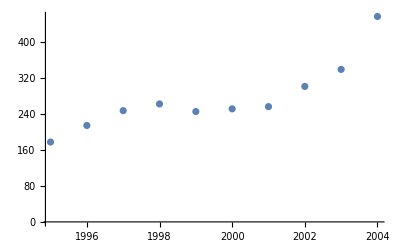

```mathematica
(* Задача 1 *)
data={
{1995,178},
{1996,215},
{1997,248},
{1998,263},
{1999,246},
{2000,252},
{2001,257},
{2002,302},
{2003,340},
{2004,458}};
dataPlot=ListPlot[data]
(* A third degree polynomial might be close to the real curve, so we will use least squares with it *)
polyDeg=3;
BasisForPolynomials[n_?NumberQ]:=Table[With[{k=k},#^k&],{k,0,n}]
polyBasis=BasisForPolynomials[polyDeg];
q=Table[Subscript[x, i],{i,0,polyDeg}];
```

```mathematica
(* а) *)
GramMatrix[basis_?ListQ, scalarProduct_]:=Table[Table[scalarProduct[basis⟦i⟧,basis⟦j⟧],{j,1,Length@basis}],{i,1,Length@basis}]
dataScalarProduct[f_,g_]:=Sum[f@data⟦i⟧⟦1⟧ g@data⟦i⟧⟦1⟧,{i,1,Length@data}]
A=Table[Table[polyBasis⟦j⟧@data⟦i⟧⟦1⟧,{j,1,Length@polyBasis}],{i,1,Length@data}];
LinearSolve[Transpose[A].A,Transpose[A].(#⟦2⟧&/@data)]

(*B=GramMatrix[polyBasis,dataScalarProduct];
LinearSolve[B,Table[Sum[data⟦i⟧⟦2⟧]]*)
```

{-27399314120212/2145,98694339589/5148,-16458527/1716,4117/2574}

{x_0→-27399314120212/2145,x_1→98694339589/5148,x_2→-16458527/1716,x_3→4117/2574}

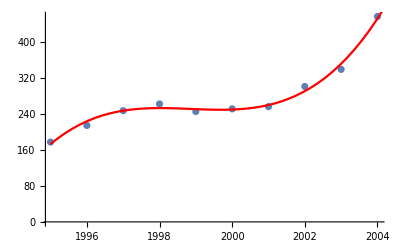

```mathematica
(* б) *)
(* {mininimum,minCoeffs}=Minimize[Sum[(q . ((#@data⟦i⟧⟦1⟧)&/@polyBasis )- data⟦i⟧⟦2⟧)^2,{i,1,Length@data}],q];
N@minCoeffs
polynomialPlot=Plot[(q/.minCoeffs).((#@x)&/@polyBasis),{x,data⟦1⟧⟦1⟧,data⟦-1⟧⟦1⟧+1},PlotStyle->Red]; *)
{mininimum,minCoeffs}=Minimize[Sum[(q . Through[polyBasis [data⟦i⟧⟦1⟧]]- data⟦i⟧⟦2⟧)^2,{i,1,Length@data}],q];
minCoeffs
polynomialPlot=Plot[(q/.minCoeffs).(Through[polyBasis[x]]),{x,data⟦1⟧⟦1⟧,data⟦-1⟧⟦1⟧+1},PlotStyle->Red]; 
Show[{dataPlot,polynomialPlot}]
```

```mathematica
(* в) *)
```

```mathematica
(* Задача 2 *)
ExampleData[{"TestImage","Lena"}];
```

-Graphics-